```mathematica
SetDirectory[NotebookDirectory[]];
<<CRNSimulator.m
```

```mathematica
?SimulateRxnsys
```

SimulateRxnsys[rxnsys,endtime] simulates the reaction system rxnsys for time 0 to endtime. In rxnsys, initial concentrations are specified by conc statements. If no initial condition is set for a species, its initial concentration is set to 0. Rxnsys can include term[] statements (eg. term[x, -2 x[t]]) which are additively combined together with term[]s derived from rxn[] statements. Rxnsys can also include ODEs directly for some species (Eg x'[t]==...) that are passed on to NDSolve without modification.
Any options specified (eg WorkingPrecision->30) are passed to NDSolve.

```mathematica
?rxn
```

Represents an irreversible reaction. eg. rxn[a+b,c,1]

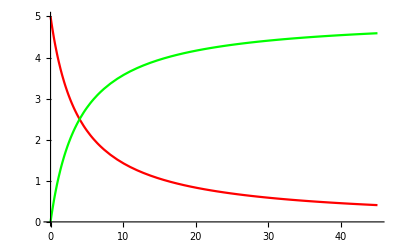

{a→InterpolatingFunction[{{0., 45.}}, <>],b→InterpolatingFunction[{{0., 45.}}, <>],c→InterpolatingFunction[{{0., 45.}}, <>]}

```mathematica
sys={
rxn[a+b,c,0.05],
conc[{a,b},5]
};
tmax=45;
sol=SimulateRxnsys[sys,tmax];
plotter={a[t],c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green},{Blue}}]
sol
```

```mathematica
?revrxn
rsys={
revrxn[a+b,c,1.5 10^6,10],
rxn[2a,b,10^5],

conc[{a,b,c},10^-9]
};
```

Represents a reversible reaction. eg. revrxn[a+b,c,1,1]

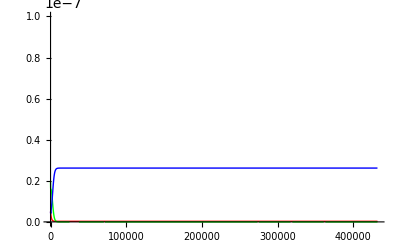

```mathematica
keff=300000;
tmax=5*24*60*60;

bibi[a_,b_,c_,d_]:=
Module[{gate,backward,agate,out,atrans,helper},
Seq[
revrxn[a+gate,backward+agate,keff/10,keff],
rxn[b+agate,out,keff],
revrxn[out+trans[c], c+atrans,keff/10,keff],
rxn[helper+atrans,d,keff],

conc[{gate,trans[c]}, 200 10^-9],
conc[backward,100 10^-9],
conc[helper, 200 10^-9]

]]
rsys=
{bibi[b,a,b,b],
bibi[c,b,c,c],

conc[b,20 10^-9],
conc[{a,c},5 10^-9]
};
sol=SimulateRxnsys[rsys,tmax];

plotSpecies=
Join[
{a,b,c},
{trans[a],trans[b],trans[c]},
SpeciesInRxnsysStringPattern[rsys,"gate$*"]];

plotter=#[t]/.sol&/@plotSpecies;
Plot[plotter,{t,0,tmax},AxesOrigin->{0,0},PlotRange->{0,100 10^-9},PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick},{Red,Thick,Dashed},{Green,Thick,Dashed},{Blue,Thick,Dashed}}]
```

```mathematica
? /@
? &
?#
?/.
```

RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"]}], "]"}] or RowBox[{StyleBox["f", "TI"], "/@", StyleBox["expr", "TI"]}] applies StyleBox["f", "TI"] to each element on the first level in StyleBox["expr", "TI"]. 
RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] applies StyleBox["f", "TI"] to parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Map", "[", StyleBox["f", "TI"], "]"}] represents an operator form of Map that can be applied to an expression.

Function[body] or body& is a pure function. The formal parameters are # (or #1), #2, etc. 
Function[x,body] is a pure function with a single formal parameter x. 
Function[{x_1,x_2,…},body] is a pure function with a list of formal parameters.

# represents the first argument supplied to a pure function. 
#n represents the n^th argument. 
#name represents the value associated with key "name" in an association in the first argument.

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr.

```mathematica
#[t]/.sol&/@plotSpecies
plotSpecies
```

{InterpolatingFunction[{{0., 432000.}}, <>][t],InterpolatingFunction[{{0., 432000.}}, <>][t],InterpolatingFunction[{{0., 432000.}}, <>][t],trans[InterpolatingFunction[{{0., 432000.}}, <>]][t],InterpolatingFunction[{{0., 432000.}}, <>][t],InterpolatingFunction[{{0., 432000.}}, <>][t],InterpolatingFunction[{{0., 432000.}}, <>][t],InterpolatingFunction[{{0., 432000.}}, <>][t]}

{a,b,c,trans[a],trans[b],trans[c],gate$23053,gate$23054}

```mathematica
?Module
?Sequence
```

RowBox[{"Module", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["expr", "TI"]}], "]"}] specifies that occurrences of the symbols StyleBox["x", "TI"], StyleBox["y", "TI"], … in StyleBox["expr", "TI"] should be treated as local. 
RowBox[{"Module", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["expr", "TI"]}], "]"}] defines initial values for StyleBox["x", "TI"], ….

Sequence[expr_1,expr_2,…] represents a sequence of arguments to be spliced automatically into any function.